# An Introduction to Mathematica

Author: Nicholas Loutrel
Date last modified: 29/11/2023

## Exercises

For the exam complete two of these... 

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_] = x Exp[-x] + x (1 - x)

f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

ⅇ^-x x+(1-x) x

0

0.180484

0.323746

0.508128

0.519463

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

{3.83,7.02,10.2}

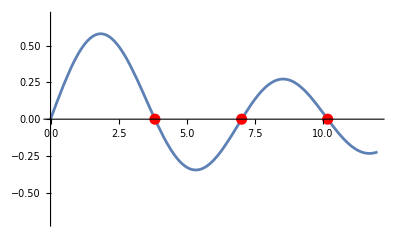

```mathematica
(*Define the Bessel function*)
BesselJ1[x_]:=BesselJ[1,x]
(*Find the first three roots*)
roots=x/. NSolve[BesselJ1[x]==0&&0<x<12,x,3]
(*Plot the Bessel function*)
Plot[BesselJ1[x],{x,0,12},PlotRange->{-0.7,0.7},Epilog->{Red,PointSize[0.02],Point[{#,0}&/@roots]}]
```

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
Clear[f]
f[x_] = Sin[x] Exp[-x]
integrate = Integrate[f[x], x]
derivative = D[integrate, x]
FullSimplify[derivative]
```

ⅇ^-x Sin[x]

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
Clear[f]
f[x_]=Exp[-ArcTan[x]]
Series[f[x], {x, ∞, 3}]
Series[f[x], {x, 0, 3}]
```

ⅇ^(-ArcTan[x])

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)+O[1/x]^4

1-x+x^2/2+x^3/6+O[x]^4

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

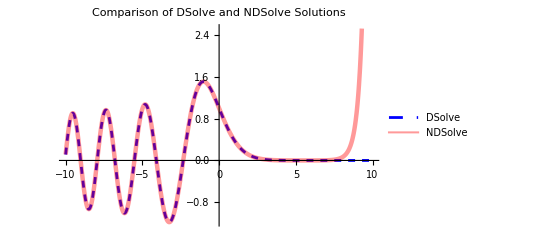

```mathematica
ClearAll["Global`*"]

eq=y''[x]-x y[x]==0;
init={y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]};

dsol=DSolve[{eq,init},y[x],x];
nsol=NDSolve[{eq,init},y,{x,-10,10}];

Plot[
Evaluate[{y[x]/. dsol,y[x]/. nsol}],{x,-10,10},
PlotStyle->{{Dashed,Blue},{Red,Thickness[0.008],Opacity[0.4]}},
PlotLegends->{"DSolve","NDSolve"},
PlotLabel->"Comparison of DSolve and NDSolve Solutions"
]
```